{0,1,2,3,4,5,6}

3 Null

{{0.92,51.21.},{0.93,60.25.},{0.94,77.35.},{0.95,84.19.},{0.96,98.13.},{0.97,167.7.},{0.98,232.41.}}

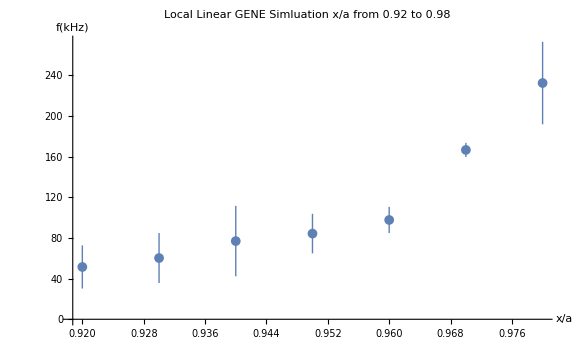

```mathematica
{Data}=Import["C:\\Users\\maxcu\\Google Drive\\0Research\\0Publication&Presentation&Poster\\Max's 1st paper\\Plots_script\\RIP\\RIP_summary"];
{nx,ny}=Dimensions[Data];
{x,y,dy}=Transpose[Data];
Plot0=Range[0,nx-1]
For[i=1,i<nx+1,i++,
Plot0[[i]]={x[[i]],Around[y[[i]],dy[[i]]]}
]3

Print [Plot0]

Show[
ListPlot[Plot0,
AxesLabel->{Style[ToExpression["\\frac{x}{a}",TeXForm,HoldForm
]
,Bold,20],
Style[ToExpression["f(kHz)",TeXForm,HoldForm
]
,Bold,20]},
PlotMarkers->{Automatic,Medium},
AxesStyle->Directive[Black,20]
],
ImageSize->Large,
PlotLabel->"Local Linear GENE Simluation x/a from 0.92 to 0.98",
BaseStyle->{FontSize->15}
]
```

```mathematica
ListPlot[rmdata,Sequence[Frame->True,FrameLabel->{"mass (kg)","radius (m)"},ScalingFunctions->{"Log",None},PlotRange->{{10^25,Automatic},Automatic},PlotMarkers->{Automatic,5},IntervalMarkersStyle->LightGray]]
```